```mathematica
ysol[d_]:=Module[{del=d},J1[delta_,w_]:=(4*((delta/(w+2^(1/6)*delta))^12-(delta/(w+2^(1/6)*delta))^6)+1)-w;U[w_]:=J1[del,w];
max=NMaximize[{-U[w],0≤w<1/2},{w},Method->"NelderMead",WorkingPrecision->150,AccuracyGoal->150];
turn=w/.NSolve[{-U[w]==max[[1]],1/2≤w},w,Reals,WorkingPrecision->150][[1]][[1]];L=4;
stest=NDSolveValue[{y''[x]-U'[y[x]]==0,y[0]==turn,y'[0]==0},y,{x,0,L},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->8,"PositionVariables"->{y[x]}},StartingStepSize->1/100000,WorkingPrecision->30,MaxSteps->Infinity];
Plot[stest[x],{x,0,4},PlotStyle->Hue[d]]]
```

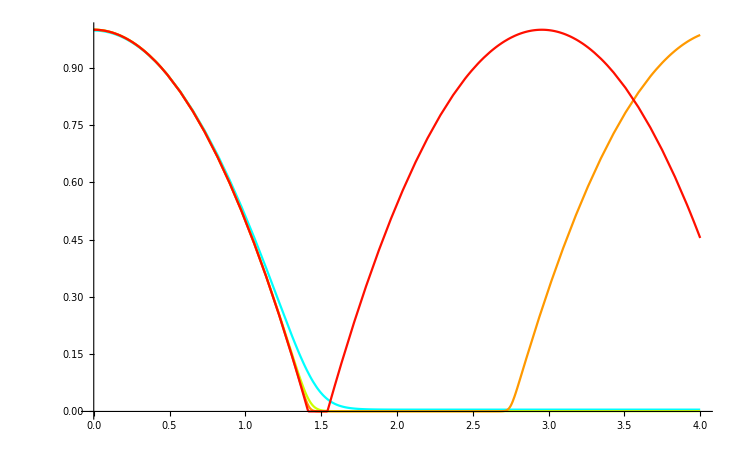

```mathematica
Show[Table[ysol[d],{d,{1/2,1/5,1/10,1/100}}]]
```

Internal`SimplifyColor::coldir: {RGBColor[0.368417, 0.506779, 0.709798],Hue[d]} contains an invalid color or gray-level directives.

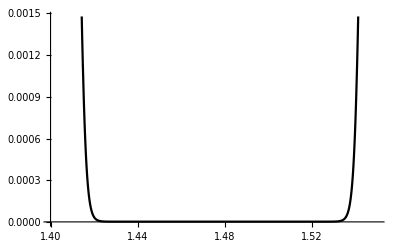

```mathematica
Plot[stest[x],{x,1.4,1.55},PlotStyle->Hue[d]]
```